```mathematica
DataSym[data_]:=Module[{l,d},d=data⟦6;;⟧;l=(Length@d)/2;Table[Around[d⟦i⟧,d⟦i+1⟧],{i,1,l-1,2}]];
DataAsym[data_]:=Module[{l,d},d=data⟦6;;⟧;l=(Length@d)/2;Table[Around[d⟦i⟧,d⟦i+1⟧],{i,l+1,2 l,2}]];
LabelName[data_]:=Module[{l,d},"β"<>ToString[data⟦1⟧]<>"_Rs"<>ToString[data⟦2⟧]<>"_λ"<>ToString[data⟦4⟧]<>"_O"<>ToString[data⟦5⟧]];
```

```mathematica
fn=FileNameJoin[{ParentDirectory@NotebookDirectory[],"F.data"}];
data=Import[fn,"Table"];
```

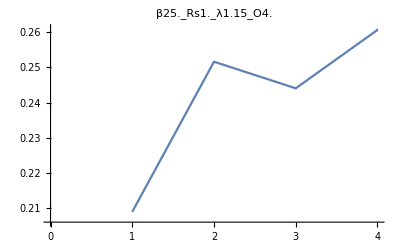
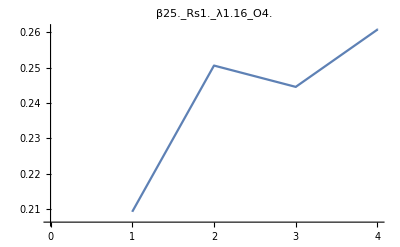
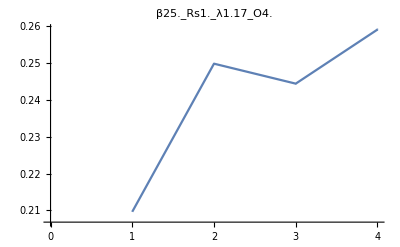
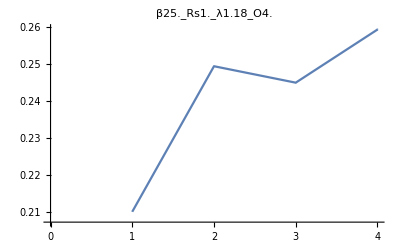
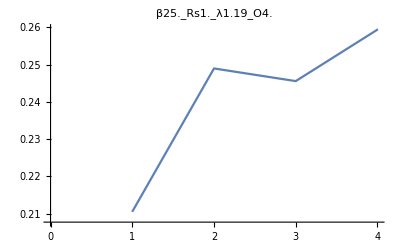
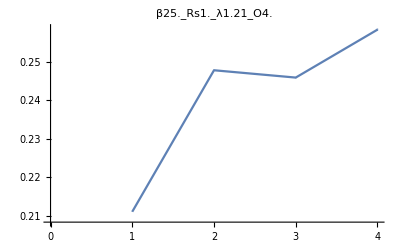
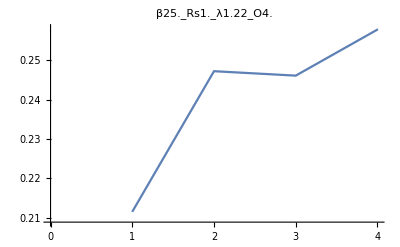
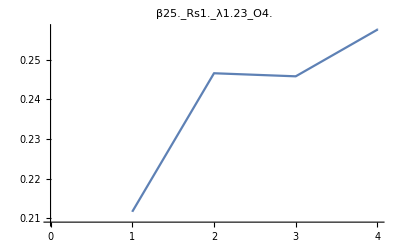

```mathematica
Table[ListPlot[DataSym[data⟦i⟧],Joined->True,PlotLabel->LabelName[data⟦i⟧]],{i,1,Length@data}]
```